# PDOS CEM1-PBE+vdWD3

Indications : You need  the CONTCAR file and the DOSCAR in the same directory before you start.

```mathematica
whereIsMyDirectory="/home/qbit/Documents/git-repositories/bachelor-thesis/cluster-files/";
(*whereIsMyDirectory="/home/hpp/wrk/mofs/poland/pc/hse/nm/";*)
nameDOSCAR="DOSCAR-cem1.sto";
nameCONTCAR="CONTCAR-cem1.rxo";
maxORB="d"(*what is the maximun orbital used? see OUTCAR*);
```

```mathematica
cordenates[in_]:=Module[{x},x=Import[in,"Table"];
Which[
x[[7,1]]=="Cartesian",
Join[{x[[6]]}, {Take[x,{8,7+Plus@@x[[6]]}]}, {x[[2,1]] Take[x,{3,5}]}],
x[[7,1]]=="Direct",Join[{x[[6]]}, {Table[Plus@@(x[[2,1]] Take[x,{3,5}]  x[[i]]),{i,8,7+Plus@@x[[6]]}]}, {x[[2,1]] Take[x,{3,5}]}] ,
x[[8,1]]=="Direct",Join[{x[[7]]},{Table[Plus@@(x[[2,1]] Take[x,{3,5}]  (x[[i]]//Take[#,3]&)),{i,9,8+Plus@@x[[7]]}]}, {x[[2,1]] Take[x,{3,5}]},{x[[6]]}],  
x[[8,1]]=="Cartesian",  Join[{x[[6]]}, {Table[x[[i]]//Take[#,3]&,{i,9,8+Plus@@x[[6]]}]}, {x[[2,1]] Take[x,{3,5}]}],
x[[9,1]]=="Direct",  Join[{x[[7]]}, {Table[Plus@@(x[[2,1]] Take[x,{3,5}]  x[[i]][[1;;3]]),{i,10,9+Plus@@x[[7]]}]}, {x[[2,1]] Take[x,{3,5}]},{x[[6]]}],
True,
Join[{x[[7]]}, {Table[x[[i]]//Take[#,3]&,{i,10,9+Plus@@x[[7]]}]}, {x[[2,1]] Take[x,{3,5}]}]]]
```

## Plotting PDOS

Note the order of OA : s, p_y, p_z, p_x, d_xy, d_yz, d_z2 - r2, d_xz, d_x2 - y2

```mathematica
SetDirectory[whereIsMyDirectory];
```

```mathematica
dosinput=Import[nameDOSCAR,"Table"];
```

```mathematica
{atomSpecies,atomicPossition,thelattice, elements}=cordenates[nameCONTCAR];
```

Check with the following command if you have the system you want :

```mathematica
{atomSpecies,elements}//Transpose
```

{{99,Ca},{60,Si},{323,O},{208,H}}

In the following you can see the total DOS with no spin polarization

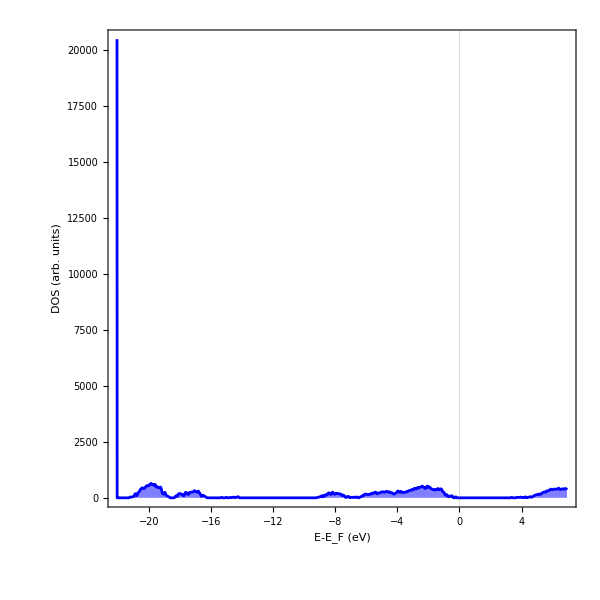

```mathematica
in=dosinput;
Ef=in[[6,4]];
NivelesNUM=in[[6,3]];
Module[{up,dwn},
up=in[[Range[7,6+NivelesNUM]]]//Map[#[[{1,2}]]-{Ef,0}&,#]&;
(*dwn=in[[Range[7,6+NivelesNUM]]]//Map[(#[[{1,3}]]-{Ef,0}) {1,-1}&,#]&;*)ListPlot[{up(*,dwn*)},Joined->True, 
Frame->True, 
Axes->False,
GridLines->{{Ef 0 },None},
FrameLabel->{"E-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
AspectRatio->1,
ImageSize->600, 
PlotRange->{{in[[6,2]],in[[6,1]]}-Ef,All}]]
```

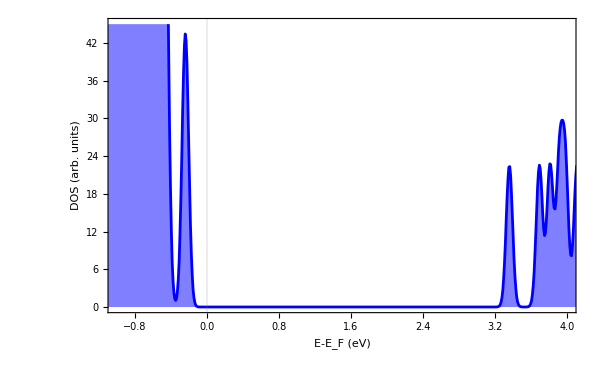

```mathematica
in=dosinput;
Ef=in[[6,4]];
NivelesNUM=in[[6,3]];
Module[{up,dwn},
up=in[[Range[7,6+NivelesNUM]]]//Map[#[[{1,2}]]-{Ef,0}&,#]&;
(*dwn=in[[Range[7,6+NivelesNUM]]]//Map[(#[[{1,3}]]-{Ef,0}) {1,-1}&,#]&;*)ListPlot[{up(*,dwn*)},Joined->True, 
Frame->True, 
Axes->False,
GridLines->{{Ef 0 },None},
FrameLabel->{"E-E_F (eV)", "DOS (arb. units)"},
BaseStyle->{"Helvetica",FontSize->15},
Filling->Axis, 
FillingStyle->Directive[Opacity[0.5],Blue],
PlotStyle->Blue,
(*AspectRatio->1,*)
ImageSize->600, 
PlotRange->{{-1,4},{0,45}}]]
```

### Creating the PDOS for specific layers

Initialize the next part before you start

```mathematica
all=Range[Plus@@atomSpecies];
Clear["pdos*"];
pdos[atom_]:=pdos[atom]=in[[Range[6+atom NivelesNUM+atom+1, 6+(atom+1) NivelesNUM+atom]]]
```

### Analysis of surface until certain thickness

Define from which deep Δz_min you need to select the atoms:

```mathematica
(*%%% INPUT AN APPROPIATE VALUE HERE %%%*)
ΔZmin=-10;
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)
```

```mathematica
surfATOMS=atomicPossition//Select[#,#[[3]]>ΔZmin&]&//Map[Position[atomicPossition,#]&,#]&//Flatten;
```

```mathematica
surfATOMS//Length
```

690

The following separate the species of atoms you selected above :

```mathematica
Table[surfATOM[i]=surfATOMS//Select[#,Plus@@(atomSpecies[[Range[i-1]]])<#≤Plus@@(atomSpecies[[Range[i]]])&]& ,{i,elements//Length}];
```

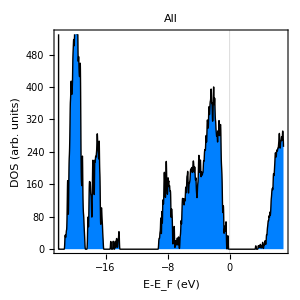
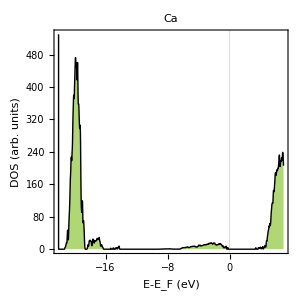
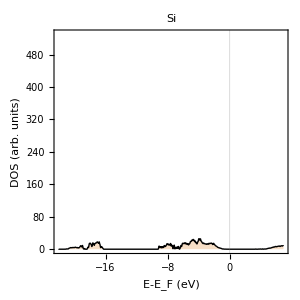
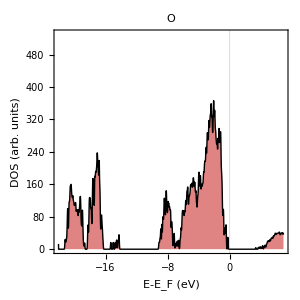
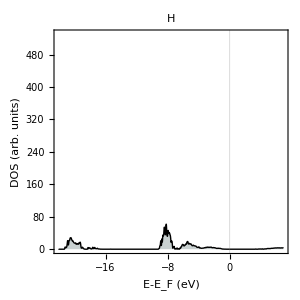

```mathematica
Join[{surfATOMS},Range[elements//Length]//Map[surfATOM[#]&,#]&]//MapIndexed[Module[{system,maxorb,elementType,color},
system=#1;
maxorb=Which[maxORB=="p", 4, maxORB=="d", 9, maxORB=="f", 16];
elementType=If[#2[[1]]==1,"All",elements[[#2[[1]]-1 ]]];
color=If[#2[[1]]==1,RGBColor[0, 0.501961, 1],Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]-1 ]]=="Ta", "Ac",elements[[#2[[1]]-1 ]] ],"IconColor"]]];
(system//Map[pdos[#]&,#]&//(Plus@@#)&)//{Map[{(#[[1]])/(system//Length)-Ef ,Plus@@(#[[Range[2,maxorb+1]]])}&,#](*,Map[{(#[[1]])/(system//Length)-Ef ,-Plus@@(#[[Range[3,9 2+1,2]]])}&,#]*)}&//ListPlot[#,
Joined->True,
Frame->True,
ImageSize->300, 
Axes->False,
GridLines->{{Ef 0},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->17},
FrameLabel->{"E-E_F (eV)", "DOS (arb. units)"},
PlotStyle->{{Black,Thin},{Black,Thin}},
Filling->Axis, 
AspectRatio->1,
FillingStyle->color,
PlotLabel->elementType,
PlotRange->{{in[[6,2]],in[[6,1]]}-Ef,{0,530}}
 ]&]&,#]&
```

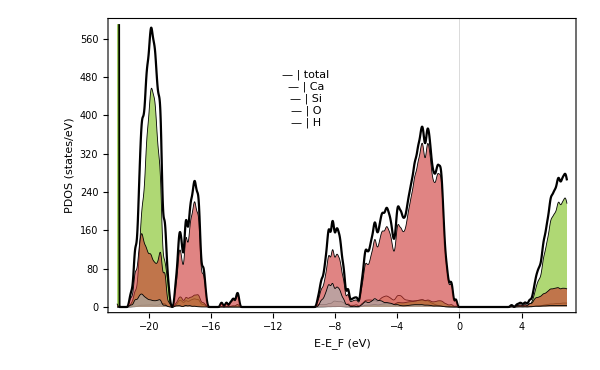

```mathematica
Join[{surfATOMS},Range[elements//Length]//Map[surfATOM[#]&,#]&]//MapIndexed[Module[{system,maxorb,type,elementType,color,fillSTYLE, plotSTYLE,gfilter},
system=#1;
maxorb=Which[maxORB=="p", 4, maxORB=="d", 9, maxORB=="f", 16];
type=First[#2];
elementType=If[#2[[1]]==1,"All",elements[[#2[[1]]-1 ]]];
color=If[#2[[1]]==1,RGBColor[0, 0.501961, 1],Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]-1 ]]=="Ta", "Ac",elements[[#2[[1]]-1 ]] ],"IconColor"]]];

plotSTYLE=Which[
type==1,RGBColor[0, 0, 0], 
True, Directive[Opacity[1],Black,Thickness[0.001]]];

(*plotSTYLE=Which[
type==1,Black, 
True, {{Black,Thin},{Black,Thin}}];*)

gfilter=15;

plot = (system//Map[pdos[#]&,#]&//(Plus@@#)&)//{Map[{#[[1]]/(system//Length)-Ef ,Plus@@(#[[Range[2,maxorb+1]]])}&,#]}&//#[[1]]&//Transpose//{#[[1]], GaussianFilter[#[[2]],gfilter]}&//Transpose//{ListPlot[#,
Joined->True,
Frame->True,
PlotTheme->"Scientific",
ImageSize->600, 
Axes->{True,True},
AxesOrigin->{0,0},
GridLines->{{Ef 0},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
FrameLabel->{"E-E_F (eV)", "PDOS (states/eV)"},
Filling->Which[type==1,None, type==2,Axis,True, Axis],
PlotStyle->plotSTYLE, 
FillingStyle->color,

(*%%%%% CHANGE THE Offset: 4.3 600/(3+7.5) IF NEEDED  %%%%%%%%%%%%%*)
Epilog->{Inset[Panel[Grid[
{
Table[Style["—", FontFamily->"TexMaths Roman",FontSize->30,FontWeight->"Bold", FontColor->If[i==0,Black,ElementData[If[elements[[i]]=="Ta","Ac",elements[[i]] ],"IconColor"]]],{i,0,elements//Length}],Join[{"total"},elements]//Map[Style[#,FontFamily->"Optima",FontSize->20]&,#]&
}//Transpose//Map[Style[#,10]&,#,{2}]&],FrameMargins->1],Offset[{-270,-80},Scaled[{1,1}]]]},
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(*%%%%% CHANGE THE RANGE HERE IF YOU NEED %%%%%%%%%%%%%*)
PlotRange->{(*{-2,3}*)All(*{-21.5,7}*),(*All*){0,590} }],
 (*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

ToString[system//Length]}&]&,#]&//
(*%%%% CHANGE values #[[1,1]] to #[[numelements+1,1]] %%%%%%%*)
Show[#[[1,1]],#[[3,1]],#[[2,1]],#[[4,1]],#[[5,1]]]&
```

```mathematica
figDir="/home/qbit/Documents/git-repositories/bachelor-thesis/figures/"
```

/home/qbit/Documents/git-repositories/bachelor-thesis/figures/

```mathematica
elements
```

{Ca,Si,O,H}

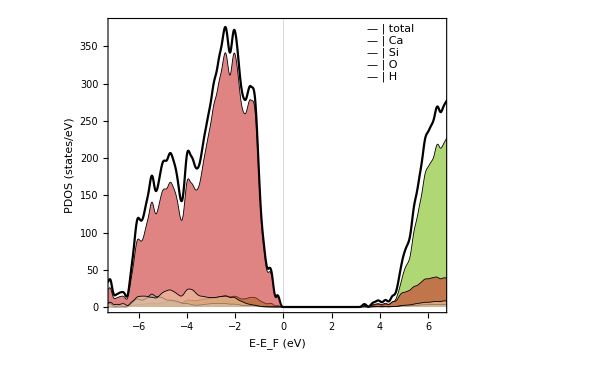

```mathematica
Join[{surfATOMS},Range[elements//Length]//Map[surfATOM[#]&,#]&]//MapIndexed[Module[{system,maxorb,type,elementType,color,fillSTYLE, plotSTYLE,gfilter},
system=#1;
maxorb=Which[maxORB=="p", 4, maxORB=="d", 9, maxORB=="f", 16];
type=First[#2];
elementType=If[#2[[1]]==1,"All",elements[[#2[[1]]-1 ]]];
color=If[#2[[1]]==1,RGBColor[0, 0.501961, 1],Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]-1 ]]=="Ta", "Ac",elements[[#2[[1]]-1 ]] ],"IconColor"]]];

plotSTYLE=Which[
type==1,RGBColor[0, 0, 0], 
True, Directive[Opacity[1],Black,Thickness[0.001]]];

(*plotSTYLE=Which[
type==1,Black, 
True, {{Black,Thin},{Black,Thin}}];*)

gfilter=15;

(system//Map[pdos[#]&,#]&//(Plus@@#)&)//{Map[{(#[[1]])/(system//Length)-Ef ,Plus@@(#[[Range[2,maxorb+1]]])}&,#]}&//#[[1]]&//Transpose//{#[[1]], GaussianFilter[#[[2]],gfilter]}&//Transpose//{ListPlot[#,
Joined->True,
Frame->True,
PlotTheme->"Scientific",
ImageSize->600, 
Axes->{True,True},
AxesOrigin->{0,0},
GridLines->{{Ef 0},None},
BaseStyle->{FontFamily->"Helvetica",FontSize->20},
FrameLabel->{"E-E_F (eV)", "PDOS (states/eV)"},
Filling->Which[type==1,None, type==2,Axis,True, Axis],
PlotStyle->plotSTYLE, 
FillingStyle->color,

(*%%%%% CHANGE THE Offset: 4.3 600/(3+7.5) IF NEEDED  %%%%%%%%%%%%%*)
Epilog->{Inset[Panel[Grid[
{
Table[Style["—", FontFamily->"Source Code Pro",FontSize->30,FontWeight->"Bold", FontColor->If[i==0,Black,ElementData[If[elements[[i]]=="Ta","Ac",elements[[i]] ],"IconColor"]]],{i,0,elements//Length}],Join[{"total"},elements]//Map[Style[#,FontFamily->"Optima",FontSize->24]&,#]&
}//Transpose//Map[Style[#,10]&,#,{2}]&],FrameMargins->1],Offset[{-80,-5},Scaled[{1,1}]],{Left,Top}]},
(*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

(*%%%%% CHANGE THE RANGE HERE IF YOU NEED %%%%%%%%%%%%%*)
PlotRange->{(*{-2,3}*){-7,6.5},(*All*){0,380} }],
 (*%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%*)

ToString[system//Length]}&]&,#]&//
(*%%%% CHANGE values #[[1,1]] to #[[numelements+1,1]] %%%%%%%*)
Show[#[[1,1]],#[[2,1]],#[[4,1]],#[[5,1]],#[[3,1]]]&
```

#### Atomic orbital (AO) components of the PDOS

The following section is for finding out the AO components of the PDOS. 
Note the order of OA : s, p_y, p_z, p_x, d_xy, d_yz, d_z2 - r2, d_xz, d_x2 - y2

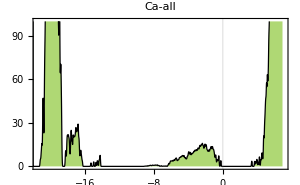
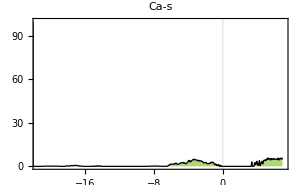
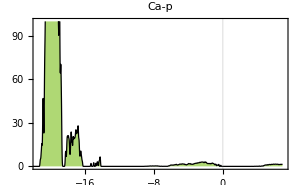
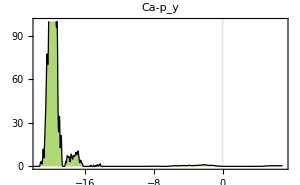
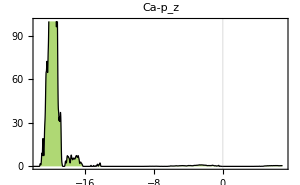
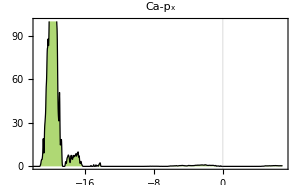
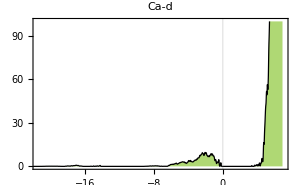
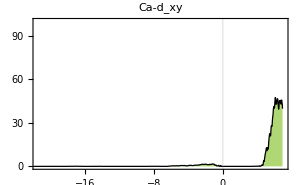

```mathematica
Join[Range[elements//Length]//Map[surfATOM[#]&,#]&]//
MapIndexed[Module[{system,maxorb,all,orbitals,s,p,py,pz,px,d,dxy,dyz,dz2,dxz,dx2y2,(*eg,t2g,f,*)color,elementType},
system=#1;
maxorb=Which[maxORB=="p", 4, maxORB=="d", 9, maxORB=="f", 16];
all={Range[2,maxorb+1],"all"};
orbitals={all,s,p,py,pz,px, d,dxy,dyz,dxz,dx2y2,dz2(*,eg,t2g,f*)};
s={{2},"s"};
p={Range[3,5,1],"p"};
py={{3},"p_y"};
pz={{4},"p_z"};
px={{5},"p_x"};
d={Range[6,10,1],"d"};
dxy={{6},"d_xy"};
dyz={{7},"d_yz"};
dz2={{8},"d_(z^2)"};
dxz={{9},"d_xz"};
dx2y2={{10},"d_(x^2)"};
(*eg={{8,10},"e_g"};*)
(*t2g={{6,7,9},"t_(2 g)"};*)
(*f={Range[11,17,1],"f"}(*Use if exist f-orbitals*);*)
color=Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]]]=="Ta", "Ac",elements[[#2[[1]]]] ],"IconColor"]];
elementType=elements[[#2[[1]] ]];
Table[(system//Map[pdos[#]&,#]&//(Plus@@#)&)//{Map[{(#[[1]])/(system//Length)-Ef ,Plus@@(#[[orbitals[[i]][[1]]]])}&,#]}&//ListPlot[#,
Joined->True,
Frame->True,
ImageSize->300, 
Axes->True,
GridLines->{{Ef 0},None},
BaseStyle->{"Helvetica",14},
PlotStyle->Directive[Black,Thickness[0.003]],
Filling->Axis, 
PlotLabel->elementType<>"-"<>orbitals[[i]][[2]],
FillingStyle->color,
PlotRange->{{-21.5,7.},{0,100}(*{0,100}*) }]&,{i,Length[orbitals]}]]&,#]&
```

# Atoms colors

```mathematica
elements
```

{Ca,Si,O,H}

```mathematica
{"Ca","Si","O","H"}//Map[Graphics[{EdgeForm[{Black,Thickness[0.08]}],ElementData[If[#=="Ti", "Ni",# ],"IconColor"],Polygon[{{0,0},{1,0},{1,1},{0,1}}]},ImageSize->40]&,#]&//GraphicsGrid[{{#[[1]]},{#[[2]]},{#[[3]]},{#[[4]]} },Spacings->Scaled[1]]&
```

-Graphics-

```mathematica
Range[1,15,2]
```

{1,3,5,7,9,11,13,15}

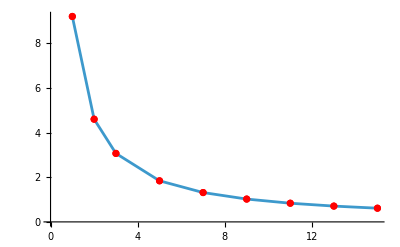

```mathematica
Table[{i,552.512/(60 i)},{i,{1,2,3,5,7,9,11,13,15}}]//ListPlot[#,Mesh->Full,MeshStyle->Red, Joined->True]&
```

```mathematica
color=If[#2[[1]]==1,RGBColor[0, 0.501961, 1],Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]-1 ]]=="Ta", "Ac",elements[[#2[[1]]-1 ]] ],"IconColor"]]]
```

Directive[Opacity[0.6],RGBColor[0.480072, 0.744591, 0.0955222]]

```mathematica
color=If[#2[[1]]==1,RGBColor[0, 0.501961, 1],Directive[Opacity[0.6],ElementData[If[elements[[#2[[1]]-1 ]]=="Ta", "Ac",elements[[#2[[1]]-1 ]] ],"IconColor"]]]
```

Directive[Opacity[0.6],RGBColor[0.480072, 0.744591, 0.0955222]]

```mathematica
colors={"Ca"->ElementData["Ca","IconColor"],(*Calcium*)"Si"->ElementData["Si","IconColor"],(*Silicon*)"O"->ElementData["O","IconColor"],(*Oxygen*)"H"->ElementData["H","IconColor"]   (*Hydrogen*)}
```

{Ca→RGBColor[0.480072, 0.744591, 0.0955222],Si→RGBColor[0.941176, 0.784314, 0.627451],O→RGBColor[0.800498, 0.201504, 0.192061],H→RGBColor[0.65, 0.7, 0.7]}

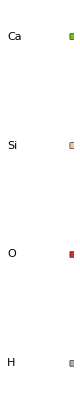

```mathematica
elements={"Ca","Si","O","H"};

GraphicsGrid[Table[{Text[Style[element,FontSize->19]],Graphics[{EdgeForm[{Black,Thickness[0.02]}],ElementData[element,"IconColor"],Rectangle[{0,0},{1,1}]},ImageSize->3]},{element,elements}],Spacings->{-23,-17},Alignment->Left]
```